# Segundo Problema Distribución Gamma

## Teoría

La variable aleatoria continua  tiene una distribución Gamma con parámetros α > 0 y λ > 0 y escribimos X \[Distributed] gamma (α, λ) si su función de densidad es

Piecewise[{{1/(Γ(α))(λx)^(α-1)λe^-λx, si}, {0, Otro caso}}]

## Corrección en Wolfram

Función Original

```mathematica
PDF[GammaDistribution[α,ξ],x]
```

Piecewise[{{(ⅇ^(-x/ξ) x^(-1+α) ξ^-α)/Gamma[α], x>0}, {0, True}}]

```mathematica
Mean[GammaDistribution[α,ξ]]
```

α ξ

```mathematica
Variance[GammaDistribution[α,ξ]]
```

α ξ^2

Función Corregida haciendo

```mathematica
PDF[GammaDistribution[α,1/λ],x]
```

Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]

```mathematica
Mean[GammaDistribution[α,1/λ]]
```

α/λ

```mathematica
Variance[GammaDistribution[α,1/λ]]
```

α/λ^2

## Distribución Gamma vs Distribución Exponencial

Sabemos que la Distribución Gamma es una generalización de la Distribución Exponencial, pues si tomamos α=1 obtenemos esa distribución, hagamos unas visualizaciones

```mathematica
PDF[GammaDistribution[1,1/λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x>0}, {0, True}}]

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
Manipulate[Plot[{PDF[GammaDistribution[1,1/λ],x],PDF[ExponentialDistribution[λ],x]},{x,0,10},Filling->Axis,PlotTheme->"Detailed"],{λ,1,10}]
```

## Graficando la Distribución Gamma variando los parámetros α y λ

```mathematica
PDF[GammaDistribution[α,1/λ],x]
```

Piecewise[{{(ⅇ^(-x λ) x^(-1+α) (1/λ)^-α)/Gamma[α], x>0}, {0, True}}]

```mathematica
x0=20;
```

```mathematica
Manipulate[Plot[PDF[GammaDistribution[α,1/λ],x],{x,1,x0},Filling->Axis],{α,1,x0},{λ,1,x0/2}]
```

## Distribución Gamma con conjuntos de datos para Media y Varianza

Generamos nuestro conjunto de datos con Distribución Gamma

```mathematica
dataGamma=RandomVariate[GammaDistribution[2,1/5],1000];
```

```mathematica
mvExacta={Mean[GammaDistribution[3,1/5]],Variance[GammaDistribution[3,1/5]]}//N
```

{0.6,0.12}

```mathematica
mvDatos={Mean[dataGamma],Variance[dataGamma]}
```

{0.562322,0.109522}

```mathematica
mvDatos-mvExacta
```

{-0.0376779,-0.0104782}

## Probabilidades

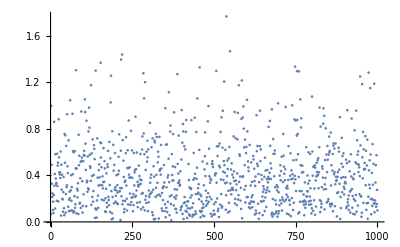

```mathematica
ListPlot[dataGamma]
```

```mathematica
Probability[x>=0.5,x\[Distributed]GammaDistribution[2,1/5]]
```

0.287297

## Histogramas

```mathematica
Manipulate[Show[Histogram[RandomVariate[GammaDistribution[α,1],1500],Automatic,"PDF"],Plot[PDF[GammaDistribution[α,1],x],{x,0,15},Filling->Axis]],{α,1,4}]
```